```mathematica
mat= Table[Import[NotebookDirectory[]<>i<>"_HH1_250_0.0_1_0.001_"<>j<>".csv"][[2]][[1]],  {i,{"ER","BA", "WS"}},{j,{"0.0","1.0e-5","0.0001","0.001","0.01"}}];
```

{{0.,168814.},{0.01,14682.6},{0.1,4049.93},{1,3063.18},{10,7055.35}}

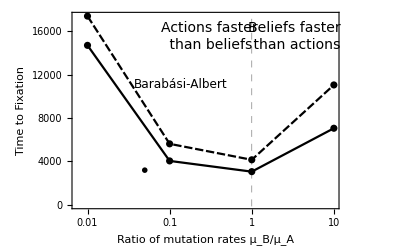

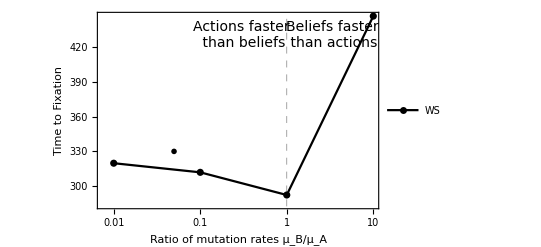

```mathematica
data1= Transpose[{{0.0,0.01,0.1,1,10},mat[[1]]}]
data2=Transpose[{{0.0,0.01,0.1,1,10},mat[[2]]}];
data3=Transpose[{{0.0,0.01,0.1,1,10},mat[[3]]}];
ListLogLinearPlot[{data1,data2},Joined->True, Mesh->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.0025]],GridLines->{{1}, None},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Monochrome",
Epilog->{
Inset[Style["Actions faster\n than beliefs",14],{-1.2,15500}],
Inset[Style["Beliefs faster\n than actions",14],{1.2,15500}],Inset[Style["Barabási-Albert",12],{-2,11100}],
Inset[Style["Erdös-Rényi",12],{-3,3200}]},FrameLabel->{Style["Ratio of mutation rates μ_B/μ_A",Black,16],Style["Time to Fixation",Black,16]},Background->White]
ListLogLinearPlot[data3,Joined->True,PlotLegends->{"WS"},Mesh->All,Frame->True,FrameStyle->Directive[Black,Thickness[0.0025]],GridLines->{{1}, None},GridLinesStyle->Directive[Gray, Dashed],PlotTheme->"Monochrome",
Epilog->{
Inset[Style["Actions faster\n than beliefs",14],{-1.2,430}],
Inset[Style["Beliefs faster\n than actions",14],{1.2,430}],
Inset[Style["Watts-Strogatz",12],{-3,330}]},FrameLabel->{Style["Ratio of mutation rates μ_B/μ_A",Black,16],Style["Time to Fixation",Black,16]},Background->White]
```

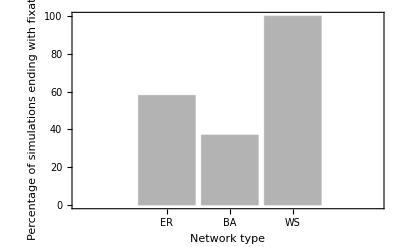

```mathematica
mat2= Table[Import[NotebookDirectory[]<>i<>"_HH1_250_0.0_1_0.001_0.0.csv"][[3]][[1]],  {i,{"ER","BA", "WS"}}];
BarChart[mat2, ChartLabels->{"ER","BA", "WS"},PlotTheme->"Monochrome" , Frame->True, FrameLabel->{Style["Network type",Black,16],Style["Percentage of simulations \n ending with fixation",Black,16]}]
```

```mathematica
networktype = "WS";
time = Table[Import[NotebookDirectory[]<>networktype<>"_HH1_250_"<>i<>"_1_0.001_"<>j<>".csv"][[2]][[1]],  {i, {"-2.0","0.0", "2.0"}},{j,{"0.01", "0.001","0.0001","1.0e-5"}}];
rescaled=#/time⟦2⟧&/@time;
transposed = Transpose[rescaled]
MatrixPlot[transposed, ColorFunction->ColorData[{"LightTemperatureMap",{0.2,2}}] ,PlotLegends->All, ColorFunctionScaling->False, DataRange->{{-2, 2},{1,2.5}}, FrameTicks->{{1,1.5,2, 2.5},{-2.0,  0.0, 2.0}}]
```

{{1.07003,1.,1.12793},{1.0028,1.,1.09659},{1.00635,1.,0.984935},{0.96767,1.,1.1972}}

-Graphics-